# 离散傅里叶变换与傅里叶级数

### 以之前任意构造的数列为例

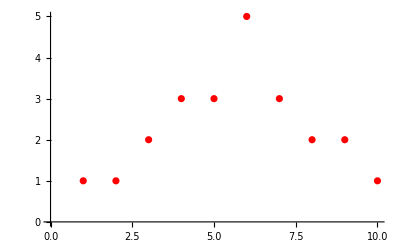

```mathematica
l={1,1,2,3,3,5,3,2,2,1};
len=Length[l]; 
lp=ListPlot[l,PlotStyle->Red]
```

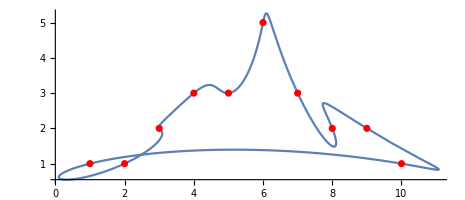

```mathematica
pts=Table[{r,l[[r]]},{r,len}];
f=Fourier[Complex@@@pts]/√len;
p=Sum[f[[Mod[n+len,len]+1]]Exp[n I t],{n,-5,4}];
Show[ParametricPlot[ReIm@p,{t,0,2π}],lp,PlotRange->All]
```

### 将上面思路包装成函数

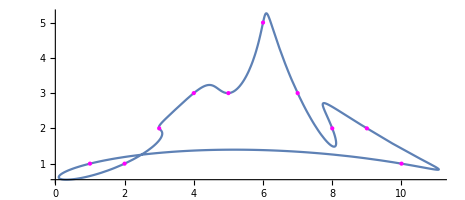

```mathematica
fPlot[l_]:=Block[{len,k,f,p},len=Length@l;
k=Ceiling[len/2];f=Fourier[Complex@@@Table[{r,l[[r]]},{r,len}]]/√len;p=Sum[f[[Mod[n+len,len]+1]]Exp[n I t],{n,k-len,k-1}];Show[ParametricPlot[ReIm@p,{t,0,2π}],ListPlot[l,PlotStyle->{Magenta,PointSize[Large]}],PlotRange->All]]
fPlot[l]
```

```mathematica
fPlot3d[l_]:=DynamicModule[{len,k,f,p},len=Length@l;
k=Ceiling[len/2];f=Fourier[Complex@@@Table[{r,l[[r]]},{r,len}]]/√len;p=Sum[f[[Mod[n+len,len]+1]]Exp[n I t],{n,k-len,k-1}];Manipulate[Show[ParametricPlot3D[{Prepend[ReIm@p,0],Prepend[ReIm@p,t]},{t,0,tt}],(*ListPlot[l,PlotStyle->{Magenta,PointSize[Large]}],*)PlotRange->10],{tt,0.01,4π}]]
fPlot3d[l]
```

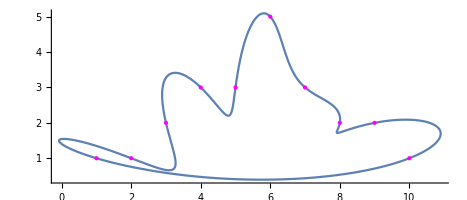

```mathematica
fPlot22[l_]:=Block[{len,k,f,p},len=Length@l;
k=Floor[len/2];f=Fourier[Complex@@@Table[{r,l[[r]]},{r,len}]]/√len;p=Sum[f[[Mod[n+len,len]+1]]Exp[n I t],{n,k-len+1,k}];Show[ParametricPlot[ReIm@p,{t,0,2π}],ListPlot[l,PlotStyle->{Magenta,PointSize[Large]}],PlotRange->All]]
fPlot22[l]
```

### 对比fPlot和fPlot22，差别在于求和范围{-5,4}和{-4,5}，换句话说当采样点的个数为偶数时，最中间的频率的相位是0或π。奇数点不存在这种差异，如下所示

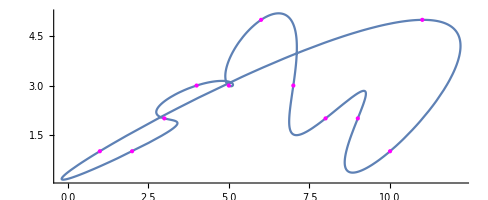

-Graphics-

```mathematica
fPlot[l~Append~5]
fPlot22[l~Append~5]
```

下面随便玩玩，感觉可以做个签名游戏

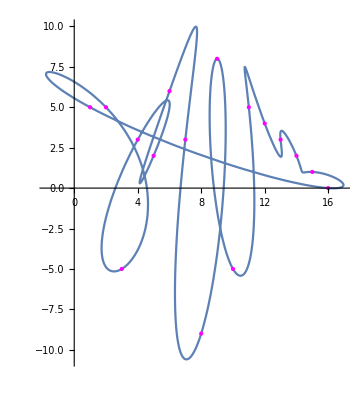

```mathematica
fPlot[{5,5,-5,3,2,6,3,-9,8,-5,5,4,3,2,1,0}]
```

### 再扩展到更一般的情况，接受以复数表示的点的坐标列表，

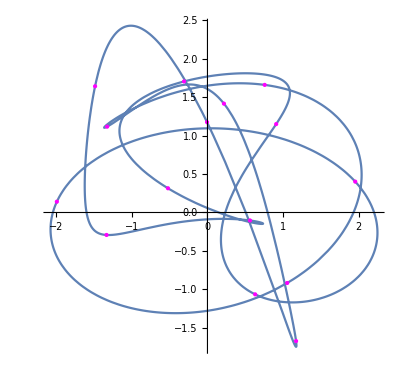

```mathematica
ePlot[cs_]:=Block[{len,k,f,p},len=Length@cs;
k=Ceiling[len/2];f=Fourier[cs]/√len;p=Sum[f[[Mod[n+len,len]+1]]Exp[n I t],{n,k-len,k-1}];Show[ParametricPlot[ReIm@p,{t,0,2π}],ListPlot[ReIm@cs,PlotStyle->{Magenta,PointSize[Large]}],PlotRange->All]]
ePlot[RandomComplex[{-2-2I,2+2I},15]]
```

## 心里蹦出两个字“完美”。

20240428  还不够